```mathematica
SetDirectory[NotebookDirectory[]];
```

# Modified basic model

## Swept of different initial metallicity values for the modified basic model (modified to have the same constants as the Ascasibar model)

## Constants

```mathematica
τS=26/10; (*[Gyr]*)
n=404754; (*[cm^-3]*)
Rh=19/10; (*[cm^3 Gyr^-1]*)
σνB=8158; (*[cm^3 Gyr^-1]*)
Zsun=134/10000;
Zeff=Zsun*10^-3;
Zsn=9/100;
ηion=95529/100;
ηdiss=38093/100;
R=18/100;
```

## Auxiliary function

```mathematica
ne=n;
nh=n;
recombination=if[t]*ne*σνB;
cloudFormation=af[t]*2*nh*Rh*((Z+Zeff)/Zsun);
ψ=mf[t]/τS;
```

## ODE system

### Initial conditions and parameters for test run and time measurement

```mathematica
if0=1/1000;
af0=500/1000;
mf0=499/1000;
sf0=0;
Ini={if0,af0,mf0,sf0,zf0};
```

```mathematica
Z = zf0;
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### System

```mathematica
var={if[t],af[t],mf[t],sf[t],zf[t]};
equ = {
if'[t]==-recombination+ηion*ψ,
af'[t]==-cloudFormation+recombination+(ηdiss-ηion)*ψ,
mf'[t]==cloudFormation-(1+ηdiss)*ψ,
sf'[t]==ψ,
zf'[t]==(Zsn*R-Z)*ψ,
if[Tstart]==if0,
af[Tstart]==af0,
mf[Tstart]==mf0,
sf[Tstart]==sf0,
zf[Tstart]==zf0
};
```

## Calculate and save solution in file

```mathematica
Zf0=Table[i,{i,0,0.03,0.0005}];
```

```mathematica
stellarF=Table[
sol=NDSolve[N[equ,60],var,{t,Tstart,Tend}][[1]];
sol=var/.sol;
(sol[[4]]/(1+sol[[4]]+sol[[5]]))/.t->1,
{zf0,Zf0}]
```

{0.227589,0.240636,0.240758,0.240758,0.240728,0.240685,0.240635,0.240583,0.240528,0.240471,0.240414,0.240356,0.240297,0.240238,0.240179,0.240119,0.240059,0.239999,0.239939,0.239879,0.239818,0.239758,0.239697,0.239637,0.239576,0.239516,0.239455,0.239395,0.239334,0.239274,0.239213,0.239152,0.239092,0.239031,0.238971,0.23891,0.23885,0.238789,0.238729,0.238668,0.238608,0.238547,0.238487,0.238426,0.238366,0.238306,0.238245,0.238185,0.238125,0.238064,0.238004,0.237944,0.237884,0.237824,0.237763,0.237703,0.237643,0.237583,0.237523,0.237463,0.237403}

```mathematica
result=MapThread[{#1,#2}&,{Zf0,stellarF}];
```

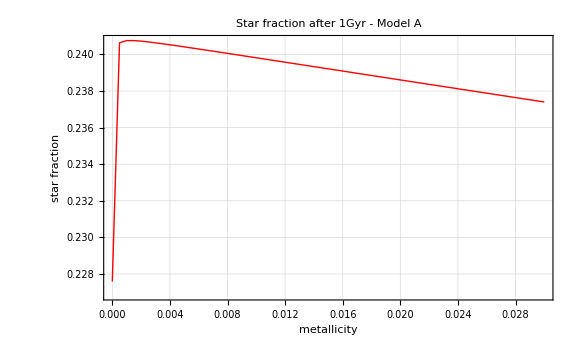

```mathematica
ListPlot[result,
Joined->True,
PlotStyle->{Thick,Red},
FrameLabel->{Style["metallicity",18],Style["star fraction",18] },
FrameStyle->Directive[Black,15],
ImageSize->Large,
Frame->True,
PlotRange->All,
GridLines->Automatic,
PlotLabel->Style["Star fraction after 1Gyr - Model A",20,Bold,Black]]
```